# ϕ^4 theory

### Initialization

Generate model files from phi4.fr by using FeynRules before doing this tutoral. See the example in “phi4_feynrules.wl”.

```mathematica
Quit[];
```

```mathematica
<<FeynArts`
<<FormCalc`
model=FileNameJoin[{NotebookDirectory[],"phi_to_four_theory_FA","phi_to_four_theory_FA"}];
(*_Hel=0;*)
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.4 (7 Jun 2016)

by Thomas Hahn

### Create Topology (and also ignore helicities)

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram



loading generic model file /Users/misho/.ghq/github.com/misho104/FeynLecture/phi_to_four_theory_FA/phi_to_four_theory_FA.gen

> $GenericMixing is OFF

generic model {/Users/misho/.ghq/github.com/misho104/FeynLecture/phi_to_four_theory_FA/phi_to_four_theory_FA} initialized

loading classes model file /Users/misho/.ghq/github.com/misho104/FeynLecture/phi_to_four_theory_FA/phi_to_four_theory_FA.mod

> 1 particles (incl. antiparticles) in 1 classes

> $CounterTerms are ON

> 1 vertices

classes model {/Users/misho/.ghq/github.com/misho104/FeynLecture/phi_to_four_theory_FA/phi_to_four_theory_FA} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

TopologyList[Process→{S[1],S[1]}→{S[1],S[1]},Model→{/Users/misho/.ghq/github.com/misho104/FeynLecture/phi_to_four_theory_FA/phi_to_four_theory_FA},GenericModel→{/Users/misho/.ghq/github.com/misho104/FeynLecture/phi_to_four_theory_FA/phi_to_four_theory_FA},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[4][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5],Field[4]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→S[1],Field[2]→S[1],Field[3]→S[1],Field[4]→S[1]]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[1],Field[2]→S[1],Field[3]→S[1],Field[4]→S[1]]]]]

> Top. 1: 1 diagram

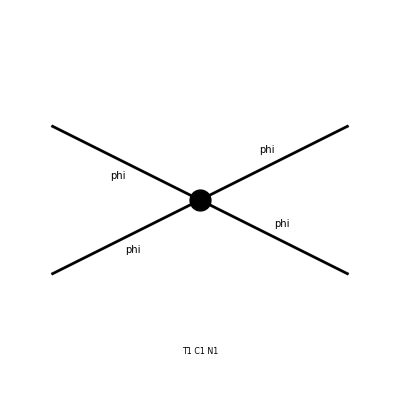

```mathematica
topo=CreateTopologies[0,2->2];
Paint[topo];
diag=InsertFields[topo,{S[1],S[1]}->{S[1],S[1]},InsertionLevel->{Classes},
Model->model,GenericModel->model]
Paint[diag];
```

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA]
SquaredME[amp]
%//FullForm
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],mmm,{}},{S[1],k[2],mmm,{}}}→{{S[1],k[3],mmm,{}},{S[1],k[4],mmm,{}}}][-lam]

lam (lamSuperscript[*])

Times[lam,Conjugate[lam]]